## Example numerical time evolution operator

Example 
H(t)= Ez(1  | 0
0 | -1)t (generally H(t) is arbitrary funtion of t)

```mathematica
H=Ez*Cos[ω*t]*PauliMatrix[1];
H//MatrixForm
```

(0 | Ez Cos[t ω]
Ez Cos[t ω] | 0)

Solve time dependent Schrödinger equation between time t0 and t1

```mathematica
u0=IdentityMatrix@Length@H;
{t0,t1}={0,10};
NDSolve[{ⅈ*D[u[t],t]==(H/.{Ez->1,ω->1}).u[t],u[t0]==u0},u[t],{t,t0,t1}]
```

{{u[t]→InterpolatingFunction[…][t]}}

Insert end time:

```mathematica
U=NDSolve[{ⅈ*D[u[t],t]==(H/.{Ez->1,ω->1}).u[t],u[t0]==u0},u[t],{t,t0,t1}][[1,1,2]]/.t->t1;
U//MatrixForm
```

(0.855634+0. ⅈ | 0.+0.517581 ⅈ
0.+0.517581 ⅈ | 0.855634+0. ⅈ)

List for different time points:

```mathematica
idlefidelitylist={};
For[i=0,i<100,i++;
u0=IdentityMatrix@Length@H;
{t0,t1}={0,0.1*i};
U=NDSolve[{ⅈ*D[u[t],t]==(H/.{Ez->1,ω->1}).u[t],u[t0]==u0},u[t],{t,t0,t1}][[1,1,2]]/.t->t1;
AppendTo[idlefidelitylist,(2+Abs[Tr[PauliMatrix[0].U]]^2)/(3*2)];
]
```

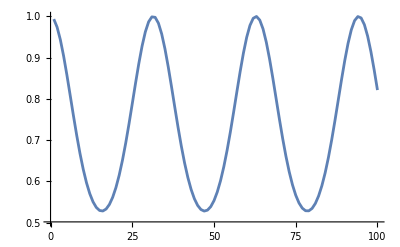

```mathematica
ListLinePlot[idlefidelitylist]
```

## Floquet Magnus Expansion

For periodic Hamiltonian H with period T the time evolution is given by
U=Exp( ∑_n Λ_n(t))Exp(∑_n F_n t)
First order corrections are
F_1=(∫_0)^T-ⅈH(τ)ⅆτ
Λ_1(t)=(∫_0)^t-ⅈH(τ)ⅆτ - F_1 t
F_2=1/2(∫_0)^T[-ⅈH(τ)+F_1,Λ_1(τ)]ⅆτ
Λ_2(t)=(∫_0)^t-ⅈH(τ)ⅆτ - F_1 t

```mathematica
F1[H_,T_]:=1/T*Integrate[-ⅈ*H/.t->τ,{τ,0,T}];
Λ1[H_,T_]:=Integrate[-ⅈ*H/.t->τ,{τ,0,t}]-F1[H,T]*t;
F2[H_,T_]:=1/(2*T)*Integrate[(-ⅈ*H+F1[H,T]).Λ1[H,T]-Λ1[H,T].(-ⅈ*H+F1[H,T])/.t->τ,{τ,0,T}];
 Λ2[H_,T_]:=1/(2)*Integrate[(-ⅈ*H+F1[H,T]).Λ1[H,T]-Λ1[H,T].(-ⅈ*H+F1[H,T])/.t->τ,{τ,0,t}]-F2[H,T]*t;
```